```mathematica
(* Diamond plot level 1: assuming no Vsd-dependence *)
figdir="/home/avery/work/phd_thesis/presentations/figures/"
wfAu=5.28;(* Work function for gold *)
zip[a_,b_]:=Table[{a[[i]],b[[i]]},{i,Length[a]}];
TElines[Vgs_,TEs_]:=Table[Fit[zip[Vgs,TEs[[i]]],{1,vg},vg],{i,Length[TEs]}];
DElines[lines_]:=Table[lines[[i+1]]-lines[[i]],{i,Length[lines]-1}]
GateCoupling[Vgs_,TEs_]:=#[[2]]&/@TElines[Vgs,TEs]/vg
ConductionChannels[vg0_,vsd_,delines_]:=Sum[If[Abs[-wfAu+delines[[i]]/.vg->vg0]≤Abs[vsd/2],1,0],{i,Length[delines]}];
DiamondPlot[delines_]:=ContourPlot[ConductionChannels[g,sd,delines],{g,-10,10},{sd,-5,5},PlotPoints->60,ColorFunction->cfun,FrameLabel->{Subscript[V, g],Subscript[V, sd]}]

cfun[x_]:=RGBColor[2.5x,x,0];
GetMoleculeLines[molecule_,dE_,exp_]:=Module[{q,Vg,Vsd,TE,Vzero},
q[x_]:=x[[1,1]];
Vg[x_]:=x[[1,2]];
Vsd[x_]:=x[[1,3]];
TE[x_]:=x[[2]];

Get["/home/avery/work/qscf-calculations/SET/results/"<>molecule<>"/"<>dE<>"/"<>exp<>".m"];
Vzero=Table[{Vg[#],TE[#]}&/@Sort[Select[propertylist,q[#]==qq&]],{qq,-2,2}];

Return[Fit[#,{1,vg},vg]&/@Vzero]
];
```

/home/avery/work/phd_thesis/presentations/figures/

```mathematica
\
```

```mathematica
Get["/home/avery/work/qscf-calculations.newold/SET/kurt-data/benzene-kurt.m"];
lkut=TElines[-Vg,TEs]
```

{-1036.99+1.17699 vg,-1039.41+0.592082 vg,-1039.53+0.00599703 vg,-1031.99-0.5836 vg,-1021.83-1.17413 vg}

{-1037.4+1.24599 vg,-1039.61+0.645235 vg,-1039.7+0.0479808 vg,-1032.12-0.550909 vg,-1022.-1.14862 vg}

{-1037.38+1.24015 vg,-1039.6+0.639823 vg,-1039.69+0.042879 vg,-1032.11-0.555663 vg,-1021.99-1.15252 vg}

{-7182.7+0.614566 vg,-7180.68+0.389965 vg,-7178.01+0.157796 vg,-7172.77-0.0400265 vg,-7166.98-0.234238 vg}

{-7179.43+0.581677 vg,-7177.4+0.35773 vg,-7174.72+0.126723 vg,-7169.53-0.0641419 vg,-7163.77-0.258903 vg}

{-8691.28+0.554013 vg,-8690.88+0.348315 vg,-8689.31+0.133311 vg,-8684.62-0.05643 vg,-8678.8-0.233794 vg}

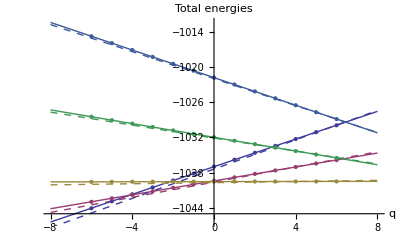

```mathematica
myl=GetMoleculeLines["benzene-kurt","0.0005","SET2-Vzero-SET"]
myl2=GetMoleculeLines["benzene-kurt","0.0005","SET2-Vzero-SET-2"]
mylopv5=GetMoleculeLines["OPV5-vnl","0.0005","Vzero-SET"]
mylopv52=GetMoleculeLines["OPV5-vnl","0.0005","Vzero-SET-2"]
mylopv5tb=GetMoleculeLines["OPV5-tertbutyl-vnl","0.0005","Vzero-SET"]

Show[Plot[lkut,{vg,-8,8}],Plot[myl,{vg,-8,8},PlotStyle->Dashed],ListPlot[zip[-Vg,#]&/@TEs],AxesLabel->{q,"Total energies"}]
```

```mathematica
dkut=DElines[lkut]
myd=DElines[myl]
(*DiamondPlot[dkut]*)
gbenzene=DiamondPlot[myd]
```

{-2.41705-0.584905 vg,-0.124053-0.586085 vg,7.53839-0.589597 vg,10.1584-0.590527 vg}

{-2.21727-0.600753 vg,-0.0894969-0.597255 vg,7.58361-0.59889 vg,10.1173-0.59771 vg}

-Graphics-

```mathematica
{mydo,mydo2,mydotbu}=DElines/@{mylopv5,mylopv52,mylopv5tb};
```

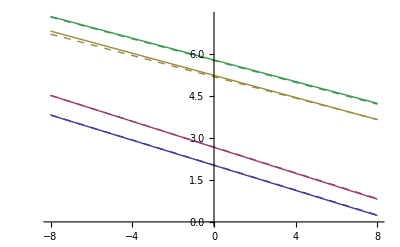

```mathematica
Show[Plot[mydo,{vg,-8,8}],Plot[mydo2,{vg,-8,8},PlotStyle->Dashed]]
```

```mathematica
mylopv5tb
```

{-8691.28+0.554013 vg,-8690.88+0.348315 vg,-8689.31+0.133311 vg,-8684.62-0.05643 vg,-8678.8-0.233794 vg}

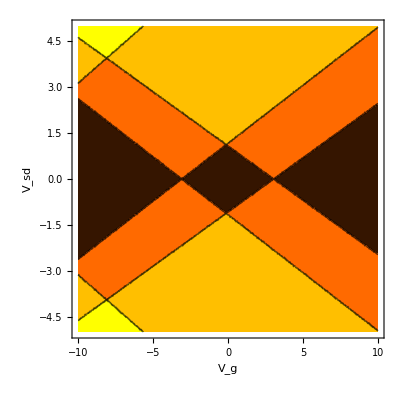

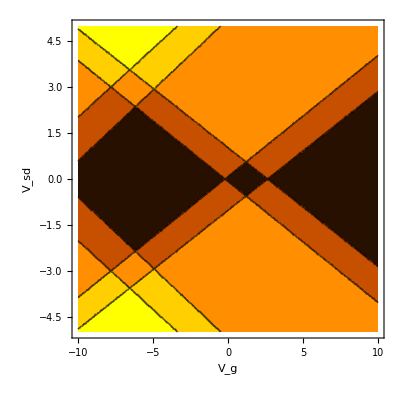

```mathematica
gobu=DiamondPlot[mydotbu]
go=DiamondPlot[mydo]
```

```mathematica
Export[figdir<>"/diamond1-benzene.png",gbenzene]
Export[figdir<>"/diamond1-opv5.png",go]
Export[figdir<>"/diamond1-opv5-tBu.png",gobu]
```

/home/avery/work/phd_thesis/presentations/figures//diamond1-benzene.png

/home/avery/work/phd_thesis/presentations/figures//diamond1-opv5.png

/home/avery/work/phd_thesis/presentations/figures//diamond1-opv5-tBu.png

```mathematica
<<PlotLegends`;
```

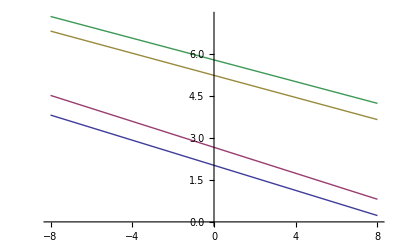

```mathematica
Plot[mydo,{vg,-8,8}]
```

```mathematica
GateCoupling[-Vg,TEs]
```

{1.17699,0.592082,0.00599703,-0.5836,-1.17413}

```mathematica
myVg=Range[-6,8,2];
myTE=#[[2]]&/@#&/@Vzero;
```

{-1037.4+1.24599 q,-1039.61+0.645235 q,-1039.7+0.0479808 q,-1032.12-0.550909 q,-1022.-1.14862 q}

```mathematica
lkut
```

{-1036.99+1.17699 q,-1039.41+0.592082 q,-1039.53+0.00599703 q,-1031.99-0.5836 q,-1021.83-1.17413 q}

```mathematica
Fit[zip[Vg,#],{1,q},q]&/@TEs
```

{-1036.99-1.17699 q,-1039.41-0.592082 q,-1039.53-0.00599703 q,-1031.99+0.5836 q,-1021.83+1.17413 q}

```mathematica
#[[7]]&/@TEs
```

{-1036.98,-1039.4,-1039.52,-1031.99,-1021.83}

{-2.41705-0.584905 vg,-0.124053-0.586085 vg,7.53839-0.589597 vg,10.1584-0.590527 vg}

{-2.21727-0.600753 vg,-0.0894969-0.597255 vg,7.58361-0.59889 vg,10.1173-0.59771 vg}

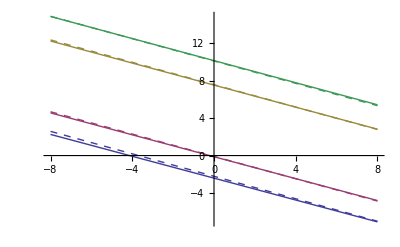

```mathematica
Show[Plot[dkut,{vg,-8,8}],Plot[myd,{vg,-8,8},PlotStyle->Dashed]]
```

```mathematica
#[[7]]&/@TEs
```

{-1036.98,-1039.4,-1039.52,-1031.99,-1021.83}

```mathematica
dkut/.vg->0
```

{-2.41705,-0.124053,7.53839,10.1584}

```mathematica
myd/.vg->0
```

{-2.21727,-0.0894969,7.58361,10.1173}

```mathematica
etheth e
```

{-10.1584,-7.53839,0.124053,2.41705}

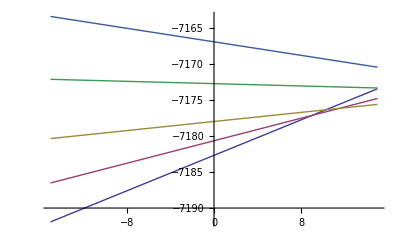

```mathematica
Plot[Evaluate[mylopv5],{vg,-15,15},PlotLegend->{"-2","-1","0","1","2"},PlotStyle->Thick,LegendSize->{.3,.3}]
```

```mathematica
?Text
```

Text[expr] displays with expr in plain text format. 
Text[expr,coords] is a graphics primitive that displays the textual form of expr centered at the point specified by coords.

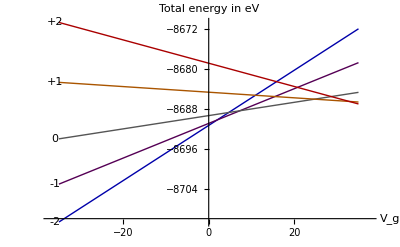

```mathematica
ll=mylopv5tb;
Vlim=35;
gTEopv5tb=Show[Plot[Evaluate[ll],{vg,-Vlim,Vlim},Axes->True,PlotRange->{{-(Vlim+2),(Vlim+2)+.6},Automatic},PlotStyle->{{Thick,Darker[Blue]},{Thick,Darker[Purple]},{Thick,Darker[Gray]},{Thick,Darker[Orange]},{Thick,Darker[Red]}}],
(*Graphics[Text["-2",{Vlim+1.3,ll[[1]]/.vg->Vlim}]],
Graphics[Text["-1",{(Vlim+1),ll[[2]]/.vg->Vlim}]],
Graphics[Text["0",{(Vlim+1)+.2,-.2+ll[[3]]/.vg->Vlim}]],Graphics[Text["+2",{(Vlim+1),ll[[5]]/.vg->Vlim}]],*)
Graphics[Text["0",{-(Vlim+1),ll[[3]]/.vg->-Vlim}]],Graphics[Text["-1",{-(Vlim+1),ll[[2]]/.vg->-Vlim}]],
Graphics[Text["-2",{-(Vlim+1),ll[[1]]/.vg->-Vlim}]],Graphics[Text["+1",{-(Vlim+1),ll[[4]]/.vg->-Vlim}]],Graphics[Text["+2",{-(Vlim+1),ll[[5]]/.vg->-Vlim}]],
AxesLabel->{Subscript[V, g],"Total energy in eV"}]
```

```mathematica
Export[figdir<>"TE-benzene.pdf",gTEbenzene]
Export[figdir<>"TE-OPV5.pdf",gTEopv5]
Export[figdir<>"TE-OPV5-tBu.pdf",gTEopv5tb]
```

/home/avery/work/phd_thesis/presentations/figures/TE-benzene.pdf

/home/avery/work/phd_thesis/presentations/figures/TE-OPV5.pdf

/home/avery/work/phd_thesis/presentations/figures/TE-OPV5-tBu.pdf

```mathematica
masto
to k
```

```mathematica
?PlotLegend
```

PlotLegend is an option for Plot, which assigns text to lines in a 2D plot to create a legend for that plot.